Autor: Adam Paździerz

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 5

Interpolacja Lagrange’a

Napisać procedurę realizującą algorytm interpolacji Lagrange’a (argumenty:  xw, yw). Działanie procedury przetestować na przykładzie z wykładu.

a) Wyznaczyć wielomian interpolacyjny przechodzący przez punkty (1,1), (2,0), (3,2), (4,3), (5,1). Wykonać ilustrację graficzną zadania.

b) Zilustrować zjawisko Rungego interpolując funkcję f(x)=|x| dla x∈ [-1,1]. Podzielić przedział na n równych części (n=2,5,10,14) i jako węzły interpolacji wybrać końce podprzedziałów. Zilustrować otrzymane wyniki.

## Rozwiązanie

### Program

```mathematica
Clear[interpolacjaLagrange];
interpolacjaLagrange[xw_,yw_]:=Module[{w,n,f},
n=Length[xw];
w=0;
For[i=1,i≤ n,i++,f=1;For[k=1,k≤i-1,k++,f=f*(x-xw⟦k⟧)/(xw⟦i⟧-xw⟦k⟧)];For[k=i+1,k≤n,k++,f=f*(x-xw⟦k⟧)/(xw⟦i⟧-xw⟦k⟧)];
w=w+yw[[i]]f];
Return[w]]
```

### Przykład testowy

```mathematica
Clear[xtest,ytest,wtest];
xtest={0,1,2};
ytest={1,0,1};
wtest=interpolacjaLagrange[xtest,ytest]
```

1/2 (1-x) (2-x)+1/2 (-1+x) x

```mathematica
Simplify[wtest]
```

(-1+x)^2

```mathematica
(*równa to się wynikowi otrzymanemu na wykładzie*)
```

### Zadanie a)

```mathematica
Clear[xa,ya,wa,Punkty,wykres1,wykres2];
xa={1,2,3,4,5};
ya={1,0,2,3,1};
wa=interpolacjaLagrange[xa,ya]
```

1/24 (2-x) (3-x) (4-x) (5-x)+1/2 (4-x) (5-x) (-2+x) (-1+x)+1/2 (5-x) (-3+x) (-2+x) (-1+x)+1/24 (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
Simplify[wa]
```

1/12 (132-204 x+101 x^2-18 x^3+x^4)

```mathematica
Punkty=List[{1,1},{2,0},{3,2},{4,3},{5,1}];
wykres1=ListPlot[Punkty,PlotStyle->Red];
wykres2=Plot[wa,{x,1,5},PlotStyle->Darker];
```

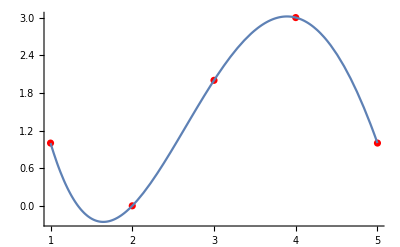

```mathematica
Show[wykres1,wykres2,PlotRange->Full]
```

### Zadanie b)

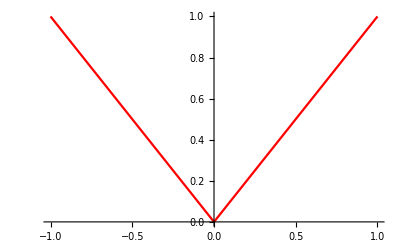

```mathematica
Clear[f];
f=Plot[Abs[x],{x,-1,1},PlotStyle->{Red}]
```

```mathematica
(*n=2*)
(*dł.przedziału/liczba podprzedziałów=2/2*)
Clear[xb2,yb2,wb2];
xb2=Table[i,{i,-1,1,1}];
yb2=Table[Abs[i],{i,-1,1,1}];
wb2=interpolacjaLagrange[xb2,yb2]
```

-1/2 (1-x) x+1/2 x (1+x)

```mathematica
Simplify[wb2]
```

x^2

```mathematica
l2=Plot[wb2,{x,-1,1},PlotStyle->Gray];
```

```mathematica
pt2=ListPlot[Transpose[{xb2,yb2}],PlotStyle->{PointSize->0.04,Pink}];
```

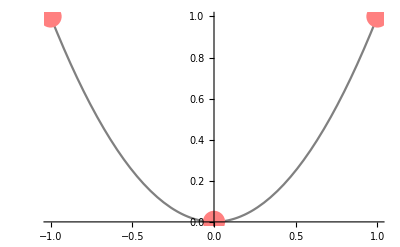

```mathematica
Show[l2,pt2]
```

```mathematica
(*n=5*)
(*dł.przedziału/liczba podprzedziałów=2/5=0.4 *)
Clear[xb5,yb5,wb5];
xb5=Table[i,{i,-1,1,0.4}];
yb5=Table[Abs[i],{i,-1,1,0.4}];
wb5=interpolacjaLagrange[xb5,yb5];
```

```mathematica
Simplify[wb5]
```

0.140625+2.22045×10^-16 x+1.51042 x^2-1.16573×10^-15 x^3-0.651042 x^4+1.11022×10^-15 x^5

```mathematica
l5=Plot[wb5,{x,-1,1}];
```

```mathematica
pt5=ListPlot[Transpose[{xb5,yb5}],PlotStyle->{PointSize->0.03,Green}];
```

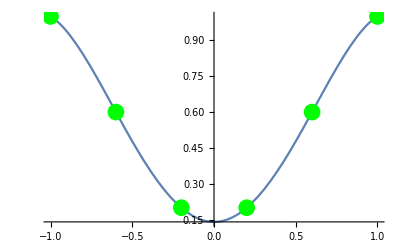

```mathematica
Show[l5,pt5]
```

```mathematica
(*n=10*)
(*dł.przedziału/liczba podprzedziałów=2/10=0.2*)
Clear[xb10,yb10,wb10];
xb10=Table[i,{i,-1,1,0.2}];
yb10=Table[Abs[i],{i,-1,1,0.2}];
wb10=interpolacjaLagrange[xb10,yb10];
```

```mathematica
Simplify[wb10]
```

0.-9.4369×10^-16 x+6.45635 x^2+1.35447×10^-14 x^3-41.2809 x^4-9.59233×10^-14 x^5+128.4 x^6+1.52767×10^-13 x^7-167.927 x^8+5.32907×10^-14 x^9+75.352 x^10

```mathematica
l10=Plot[wb10,{x,-1,1},PlotStyle->Pink];
pt10=ListPlot[Transpose[{xb10,yb10}],PlotStyle->{PointSize->0.01,Blue}];
```

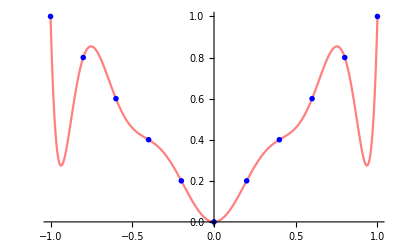

```mathematica
Show[l10,pt10]
```

```mathematica
(*n=14*)
(*dł.przedziału/liczba podprzedziałów=2/14*)
```

```mathematica
Clear[xb14,yb14,wb14];
xb14=Table[i,{i,-1,1,2/14}];
yb14=Table[Abs[i],{i,-1,1,2/14}];
wb14=interpolacjaLagrange[xb14,yb14];
```

```mathematica
Simplify[wb14]
```

1/74131200 x^2 (683628480-9377776408 x^2+69040097126 x^4-254493728489 x^6+478956961483 x^8-436989210203 x^10+152254159211 x^12)

```mathematica
l14=Plot[wb14,{x,-1,1},PlotStyle->Orange];
pt14=ListPlot[Transpose[{xb14,yb14}],PlotStyle->{PointSize->0.02}];
```

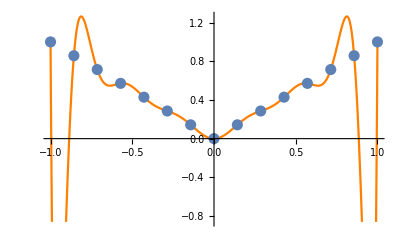

```mathematica
Show[l14,pt14]
```

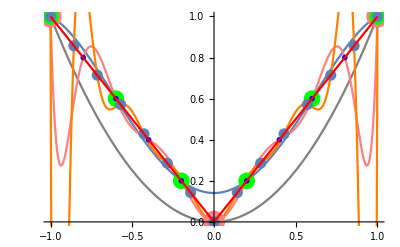

```mathematica
Show[l2,l5,l10,l14,pt2,pt5,pt10,pt14,f]
```